## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"]
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

## 设置non-GR参数字符flag Gw@150914!

```mathematica
eventID="GW151012";

deviationType="cpsi";
deviationOrders=List[0,2,3,4,"5l",6,"6l"];
deviationNames=List["cpsi0","cpsi2","cpsi3","cpsi4","cpsi5l","cpsi6","cpsi6l"];
psiNames=List["psi0","psi2","psi3","psi4","psi5l","psi6","psi6l"];

deviationType="cpsi";
deviationOrders=List[0,2,4,"5l",6,"6l",7];
deviationNames=List["cpsi0","cpsi2","cpsi4","cpsi5l","cpsi6","cpsi6l","cpsi7"];
psiNames=List["psi0","psi2","psi4","psi5l","psi6","psi6l","psi7"];
```

```mathematica
csvPath="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv"<>"\\"<>eventID;
csvNames=eventID<>"_"<>#<>".csv"& /@ deviationNames;

csvFilePaths=csvPath<>"\\"<>#& /@ csvNames;
```

### from CSV

```mathematica
samples=<||>;
Do[
CSVSamples=Import["D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv\\"<>eventID<>"\\"<>eventID<>"_"<>n<>".csv"];
samples[n]=<||>;
samples[n]["mass1"]=CSVSamples[[All,1]][[2;;]];
samples[n]["mass2"]=CSVSamples[[All,2]][[2;;]];
samples[n]["spin1z"]=CSVSamples[[All,3]][[2;;]];
samples[n]["spin2z"]=CSVSamples[[All,4]][[2;;]];
samples[n]["eta"]=CSVSamples[[All,5]][[2;;]];
samples[n]["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[n][n]=CSVSamples[[All,7]][[2;;]];
samples[n]["chis"]=χs[samples["spin1z"],samples["spin2z"]];
samples[n]["chia"]=χa[samples["spin1z"],samples["spin2z"]];,
{n,deviationNames}
]
```

### Calculate GR Coefficients

```mathematica
Do[
samples[deviationNames[[n]]][psiNames[[n]]]=MapThread[
Psi[deviationOrders[[n]],η[#1,#2],M[#1,#2],#3,#4]&,
{samples[deviationNames[[n]]]["mass1"],samples[deviationNames[[n]]]["mass2"],samples[deviationNames[[n]]]["spin1z"],samples[deviationNames[[n]]]["spin2z"]}
];,
{n,Range[Length[deviationOrders]]}
]
```

### Calculate BCIs

```mathematica
BCI=<||>;
Do[
BCI[deviationNames[[n]]]=<||>;
BCI[deviationNames[[n]]]["mass1"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass1"],Subscript["m","1"]][[1]];
BCI[deviationNames[[n]]]["mass2"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass2"],Subscript["m","2"]][[1]];
BCI[deviationNames[[n]]]["spin1z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin1z"],"spin1z"][[1]];
BCI[deviationNames[[n]]]["spin2z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin2z"],"spin2z"][[1]];
BCI[deviationNames[[n]]][deviationNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][deviationNames[[n]]],deviationNames[[n]]][[1]];
BCI[deviationNames[[n]]][psiNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][psiNames[[n]]],psiNames[[n]]][[1]];,
{n,Range[Length[deviationOrders]]}
]
```

```mathematica
widths={};
Do[
AppendTo[widths,(BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]])/(BCI[deviationNames[[n]]][psiNames[[n]]][[3]]-BCI[deviationNames[[n]]][psiNames[[n]]][[1]])],
{n,Range[Length[deviationOrders]]}
];
Round[widths,0.0001]
widths={};
Do[
AppendTo[widths,BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]]],
{n,Range[Length[deviationOrders]]}
];
Round[widths/{5000,250,150,5,1.5,0.5,0.1},0.0001]
```

{0.2849,2.5701,16.4063,4.1174,3.2651,11.5891,2.0944}

{0.7044,4.8795,3.8411,11.7879,35.8945,20.7757,80.6611}

```mathematica
o="5l";
{Quantile[samples["cpsi"<>o]["psi"<>o],{0.05,0.95}]-Median[samples["cpsi"<>o]["psi"<>o]],Median[samples["cpsi"<>o]["psi"<>o]]}
```

{{-6.76718,7.54746},3.16977}

```mathematica
medians={};
Do[
AppendTo[medians,BCI[deviationNames[[n]]][deviationNames[[n]]][[2]]/BCI[deviationNames[[n]]][psiNames[[n]]][[2]]],
{n,Range[Length[deviationOrders]]}
];
Round[medians,0.0001]
```

{1.0255,2.8484,16.8189,-31.011,-23.1788,15.0297,-5.2003}

## m1-m2 Plot, 22

```mathematica
pInterval=<||>;
tapeIntervals=<||>;
tapes=<||>;
plots=<||>;
compPlots=<||>;
lines=<||>;
legends=<||>;

m1m2=<||>;
m1PriorRange=<||>;
m2PriorRange=<||>;
m1m2PDF=<||>;
contourPD=<||>;
contourPlotObj=<||>;
contourPoints=<||>;
smoothedContourPoints=<||>;
```

```mathematica
BCI
```

<|cpsi0→<|mass1→{27.8001,45.4635,56.164},mass2→{7.5888,11.0762,19.285},spin1z→{0.0669802,0.570596,0.83343},spin2z→{-0.859887,0.231708,0.898089},cpsi0→{15657.4,18325.4,19360.},psi0→{14939.4,18206.3,27807.}|>,cpsi2→<|mass1→{22.5562,38.5337,58.7621},mass2→{7.87779,12.3079,17.9034},spin1z→{-0.0115364,0.533351,0.84644},spin2z→{-0.893286,-0.241835,0.593196},cpsi2→{1920.93,2483.56,3155.07},psi2→{898.156,996.398,1302.55}|>,cpsi6l→<|mass1→{26.1185,40.2256,52.8701},mass2→{9.96719,13.5835,19.7334},spin1z→{0.125456,0.618524,0.874937},spin2z→{-0.902033,-0.438706,0.480844},cpsi6l→{-23.3249,-19.0778,-12.9436},psi6l→{-1.83024,-1.26922,-0.933476}|>|>

### 0/2PN

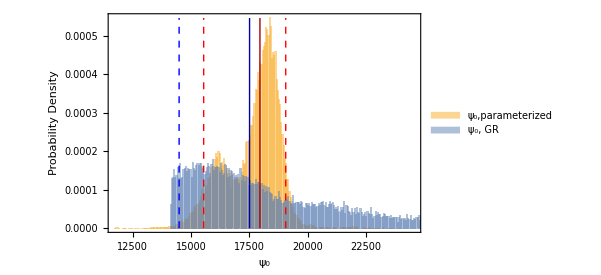

输入Mc范围：{11,22}

输入q范围：{1,12}

m1范围：{12.6357,99.285}

m2范围：{4.13688,25.2714}

原始数据量 = 95037，降采样后数据量 = 95037（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999962

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 7.72159×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.0085}

等高线数量：1 条

第一条等高线的前5个边界点：{{45.1505,12.8119},{46.6765,13.1241},{47.0517,13.103},{48.5178,12.8888},{49.1837,12.583}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$2956352条等高线 =====

包含闭合区域数：1

区域内总积分值：0.0581167

可信水平百分比：5.81167%

==========================

```mathematica
order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{11,22},{1,12}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0085};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

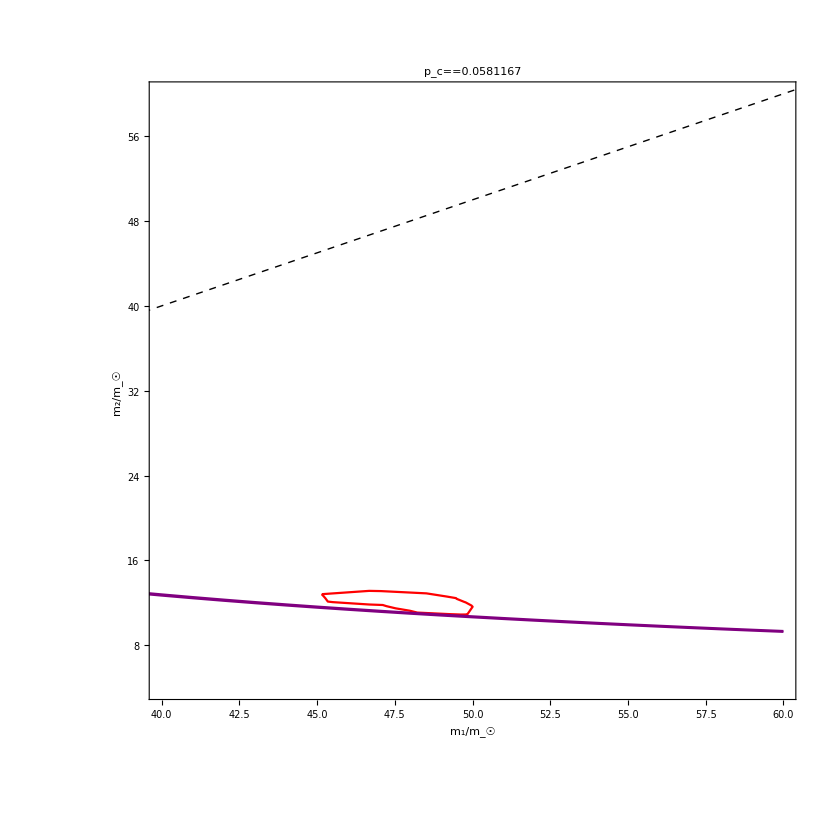

```mathematica
m1s=Range[40,60,1];
m2s=Range[4,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

### 2/2PN

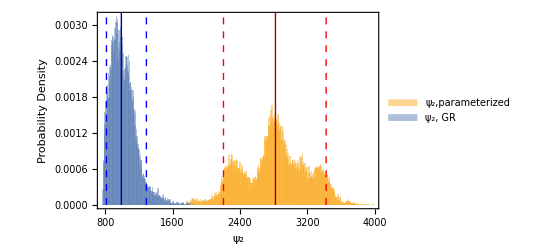

输入Mc范围：{11,22}

输入q范围：{1,12}

m1范围：{12.6357,99.285}

m2范围：{4.13688,25.2714}

原始数据量 = 93623，降采样后数据量 = 93623（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999812

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 7.49955×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.0009}

等高线数量：1 条

第一条等高线的前5个边界点：{{59.055,5.258},{57.163,5.64648},{56.5341,5.78642},{55.9604,6.00316},{55.8846,6.02388}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$2970216条等高线 =====

包含闭合区域数：1

区域内总积分值：0.907655

可信水平百分比：90.7655%

==========================

```mathematica
order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{11,22},{1,12}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0009};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

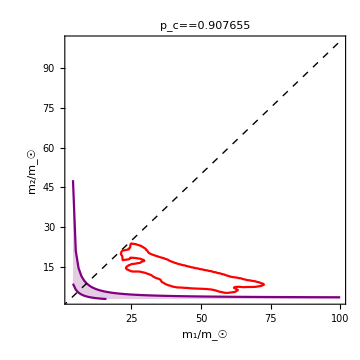

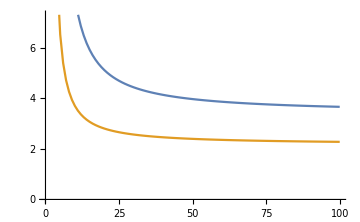

```mathematica
m1s=Range[3,100,1];
m2s=Range[3,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

```mathematica
contourPoints[n]
```

{{{26.6694,18.2442},{26.9285,18.117},{27.3117,17.9143},{27.7305,17.5021},{27.7369,17.4961},{27.75,17.4838},{28.2861,17.1351},{29.0799,16.7824},{29.6289,16.5262},{31.5282,16.3701},{31.7397,16.3558},{31.8925,16.3431},{32.3437,16.2724},{33.0696,16.2103},{33.99,16.0831},{34.3995,15.9537},{35.4884,15.6575},{35.6645,15.6275},{35.994,15.5352},{37.0593,15.3253},{37.5313,15.2609},{38.0134,15.0427},{38.2656,14.9855},{38.3892,14.9626},{39.2292,14.8162},{39.7191,14.6304},{40.4103,14.4278},{40.8646,14.3426},{41.049,14.2962},{41.5942,14.1757},{41.7139,14.1546},{41.7723,14.1474},{41.8769,14.1204},{42.2248,14.0609}}}

### 3/2PN

```mathematica
(*order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{11,22},{1,12}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0009};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];*)
```

```mathematica
(*m1s=Range[3,100,1];
m2s=Range[3,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]*)
```

### 4/2PN

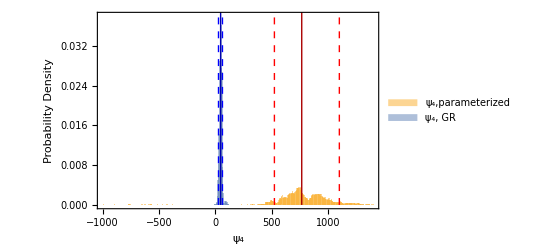

输入Mc范围：{11,22}

输入q范围：{1,12}

m1范围：{12.6357,99.285}

m2范围：{4.13688,25.2714}

原始数据量 = 58864，降采样后数据量 = 58864（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999725

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 8.70031×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.0002}

等高线数量：2 条

第一条等高线的前5个边界点：{{48.6381,4.3957},{48.6864,4.40144},{48.9975,4.43468},{49.6746,4.51428},{49.7398,4.52193}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

===== 第i$3264154条等高线 =====

包含闭合区域数：2

区域内总积分值：0.987062

可信水平百分比：98.7062%

==========================

```mathematica
order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{11,22},{1,12}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0002};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[-1]][[2]];
```

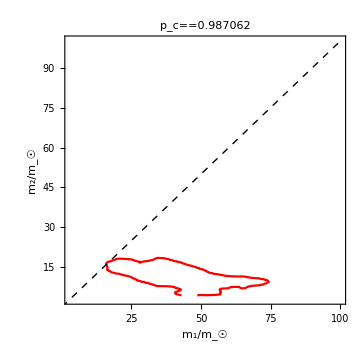

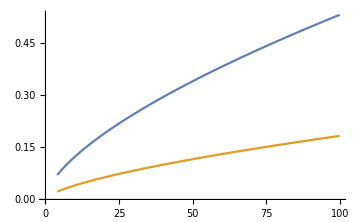

```mathematica
m1s=Range[3,100,1];
m2s=Range[3,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

### 5/2PN, log

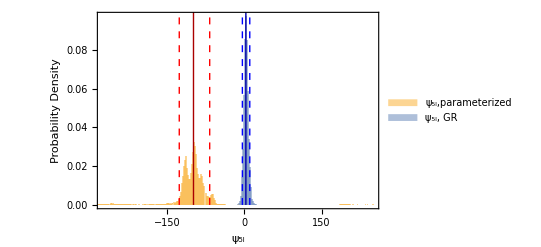

输入Mc范围：{11,22}

输入q范围：{1,12}

m1范围：{12.6357,99.285}

m2范围：{4.13688,25.2714}

原始数据量 = 56729，降采样后数据量 = 56729（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999998

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 9.33805×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.0001}

等高线数量：1 条

第一条等高线的前5个边界点：{{33.1549,8.38687},{32.9399,8.24214},{32.0882,7.91089},{33.0683,7.61096},{34.298,7.30398}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$3277553条等高线 =====

包含闭合区域数：1

区域内总积分值：0.997208

可信水平百分比：99.7208%

==========================

```mathematica
order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{11,22},{1,12}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

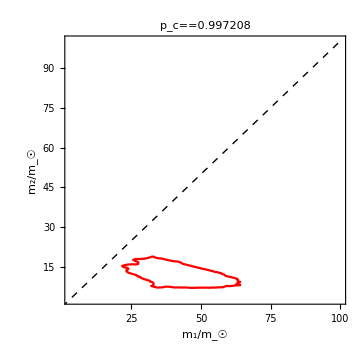

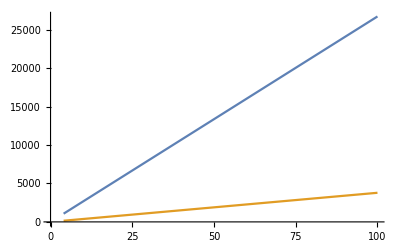

```mathematica
m1s=Range[3,100,1];
m2s=Range[3,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

```mathematica
tapes[n][n][[1]][[2;;]]
```

{{4,1068.73},{5,1335.92},{6,1603.1},{7,1870.28},{8,2137.47},{9,2404.65},{10,2671.83},{11,2939.02},{12,3206.2},{13,3473.38},{14,3740.57},{15,4007.75},{16,4274.93},{17,4542.12},{18,4809.3},{19,5076.48},{20,5343.67},{21,5610.85},{22,5878.03},{23,6145.22},{24,6412.4},{25,6679.58},{26,6946.77},{27,7213.95},{28,7481.13},{29,7748.32},{30,8015.5},{31,8282.68},{32,8549.87},{33,8817.05},{34,9084.23},{35,9351.42},{36,9618.6},{37,9885.78},{38,10153.},{39,10420.2},{40,10687.3},{41,10954.5},{42,11221.7},{43,11488.9},{44,11756.1},{45,12023.3},{46,12290.4},{47,12557.6},{48,12824.8},{49,13092.},{50,13359.2},{51,13626.4},{52,13893.5},{53,14160.7},{54,14427.9},{55,14695.1},{56,14962.3},{57,15229.5},{58,15496.6},{59,15763.8},{60,16031.},{61,16298.2},{62,16565.4},{63,16832.6},{64,17099.7},{65,17366.9},{66,17634.1},{67,17901.3},{68,18168.5},{69,18435.7},{70,18702.8},{71,18970.},{72,19237.2},{73,19504.4},{74,19771.6},{75,20038.8},{76,20305.9},{77,20573.1},{78,20840.3},{79,21107.5},{80,21374.7},{81,21641.9},{82,21909.},{83,22176.2},{84,22443.4},{85,22710.6},{86,22977.8},{87,23245.},{88,23512.1},{89,23779.3},{90,24046.5},{91,24313.7},{92,24580.9},{93,24848.1},{94,25115.2},{95,25382.4},{96,25649.6},{97,25916.8},{98,26184.},{99,26451.2},{100,26718.3}}

```mathematica
tapes[n][n][[2]][[2;;]]
```

{{4,151.457},{5,189.321},{6,227.185},{7,265.049},{8,302.913},{9,340.777},{10,378.642},{11,416.506},{12,454.37},{13,492.234},{14,530.098},{15,567.962},{16,605.827},{17,643.691},{18,681.555},{19,719.419},{20,757.283},{21,795.147},{22,833.012},{23,870.876},{24,908.74},{25,946.604},{26,984.468},{27,1022.33},{28,1060.2},{29,1098.06},{30,1135.92},{31,1173.79},{32,1211.65},{33,1249.52},{34,1287.38},{35,1325.25},{36,1363.11},{37,1400.97},{38,1438.84},{39,1476.7},{40,1514.57},{41,1552.43},{42,1590.29},{43,1628.16},{44,1666.02},{45,1703.89},{46,1741.75},{47,1779.62},{48,1817.48},{49,1855.34},{50,1893.21},{51,1931.07},{52,1968.94},{53,2006.8},{54,2044.66},{55,2082.53},{56,2120.39},{57,2158.26},{58,2196.12},{59,2233.99},{60,2271.85},{61,2309.71},{62,2347.58},{63,2385.44},{64,2423.31},{65,2461.17},{66,2499.03},{67,2536.9},{68,2574.76},{69,2612.63},{70,2650.49},{71,2688.36},{72,2726.22},{73,2764.08},{74,2801.95},{75,2839.81},{76,2877.68},{77,2915.54},{78,2953.4},{79,2991.27},{80,3029.13},{81,3067.},{82,3104.86},{83,3142.73},{84,3180.59},{85,3218.45},{86,3256.32},{87,3294.18},{88,3332.05},{89,3369.91},{90,3407.77},{91,3445.64},{92,3483.5},{93,3521.37},{94,3559.23},{95,3597.1},{96,3634.96},{97,3672.82},{98,3710.69},{99,3748.55},{100,3786.42}}

### 6/2PN; no solution

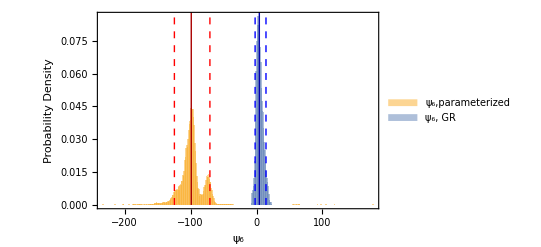

输入Mc范围：{11,22}

输入q范围：{1,12}

m1范围：{12.6357,99.285}

m2范围：{4.13688,25.2714}

原始数据量 = 58493，降采样后数据量 = 58493（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999997

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 4.5279×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.001}

等高线数量：1 条

第一条等高线的前5个边界点：{{34.298,11.3861},{33.6962,11.5381},{33.3588,11.6849},{32.7507,11.826},{32.1402,11.9134}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$3281999条等高线 =====

包含闭合区域数：1

区域内总积分值：0.930315

可信水平百分比：93.0315%

==========================

```mathematica
order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{11,22},{1,12}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

0.7

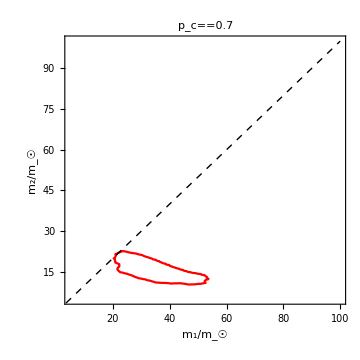

-Graphics-

```mathematica
m1s=Range[5,100,1];
m2s=Range[5,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

### 6/2PN, log

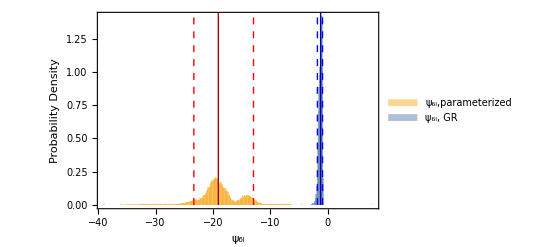

输入Mc范围：{11,22}

输入q范围：{1,12}

m1范围：{12.6357,99.285}

m2范围：{4.13688,25.2714}

原始数据量 = 94475，降采样后数据量 = 94475（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999995

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.321×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-7}

等高线数量：2 条

第一条等高线的前5个边界点：{{50.468,4.40338},{50.5448,4.43655},{50.6912,4.51428},{51.0159,4.58807},{51.0279,4.70298}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$3296323条等高线 =====

包含闭合区域数：2

区域内总积分值：0.555864

可信水平百分比：55.5864%

==========================

```mathematica
order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{11,22},{1,12}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[-1]][[2]];
```

```mathematica
prob
```

0.555864

0.99

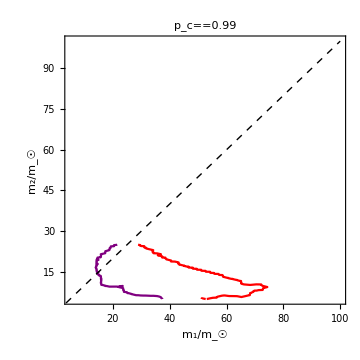

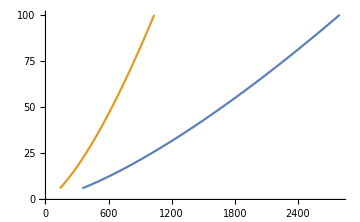

```mathematica
prob=0.99
m1s=Range[5,100,1];
m2s=Range[5,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],
contourPoints[n][[2]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

### 7/2PN

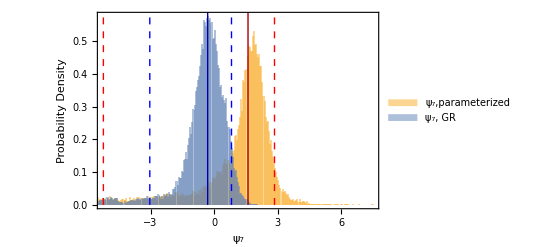

输入Mc范围：{11,22}

输入q范围：{1,12}

m1范围：{12.6357,99.285}

m2范围：{4.13688,25.2714}

原始数据量 = 104185，降采样后数据量 = 104185（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999997 and 5.77692×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999997（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.01}

等高线数量：1 条

第一条等高线的前5个边界点：{{21.9195,13.0021},{21.618,13.121},{21.5569,13.1945},{21.3779,13.3266},{20.743,13.6624}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$3569890条等高线 =====

包含闭合区域数：1

区域内总积分值：0.542953

可信水平百分比：54.2953%

==========================

```mathematica
order=7;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{11,22},{1,12}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.01};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

0.2

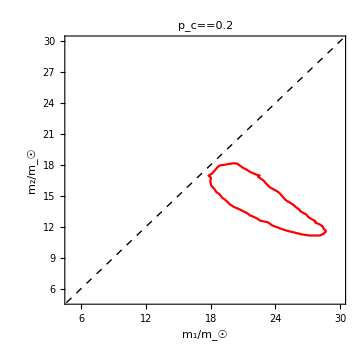

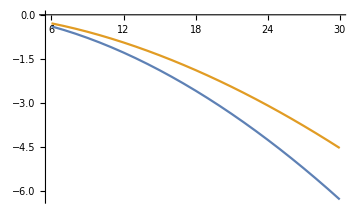

```mathematica
prob=0.2
m1s=Range[5,30,1];
m2s=Range[5,30,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

```mathematica
tapes[n][n][[1]][[2;;]]
```

{{31,-14.4288+77.9341 ⅈ},{32,-14.5746+79.3581 ⅈ},{33,-14.715+80.7605 ⅈ},{34,-14.8503+82.1423 ⅈ},{35,-14.9807+83.5042 ⅈ},{36,-15.1064+84.8469 ⅈ},{37,-15.2276+86.1711 ⅈ},{38,-15.3445+87.4774 ⅈ},{39,-15.4572+88.7664 ⅈ},{40,-15.566+90.0386 ⅈ},{41,-15.6709+91.2946 ⅈ},{42,-15.772+92.5349 ⅈ},{43,-15.8696+93.7599 ⅈ},{44,-15.9637+94.9701 ⅈ},{45,-16.0544+96.1658 ⅈ},{46,-16.1419+97.3475 ⅈ},{47,-16.2263+98.5155 ⅈ},{48,-16.3076+99.6702 ⅈ},{49,-16.3859+100.812 ⅈ},{50,-16.4614+101.941 ⅈ},{51,-16.534+103.058 ⅈ},{52,-16.604+104.162 ⅈ},{53,-16.6713+105.255 ⅈ},{54,-16.736+106.337 ⅈ},{55,-16.7982+107.407 ⅈ},{56,-16.858+108.466 ⅈ},{57,-16.9153+109.514 ⅈ},{58,-16.9704+110.551 ⅈ},{59,-17.0231+111.579 ⅈ},{60,-17.0736+112.596 ⅈ}}

Part::partw: Part 7 of … does not exist.

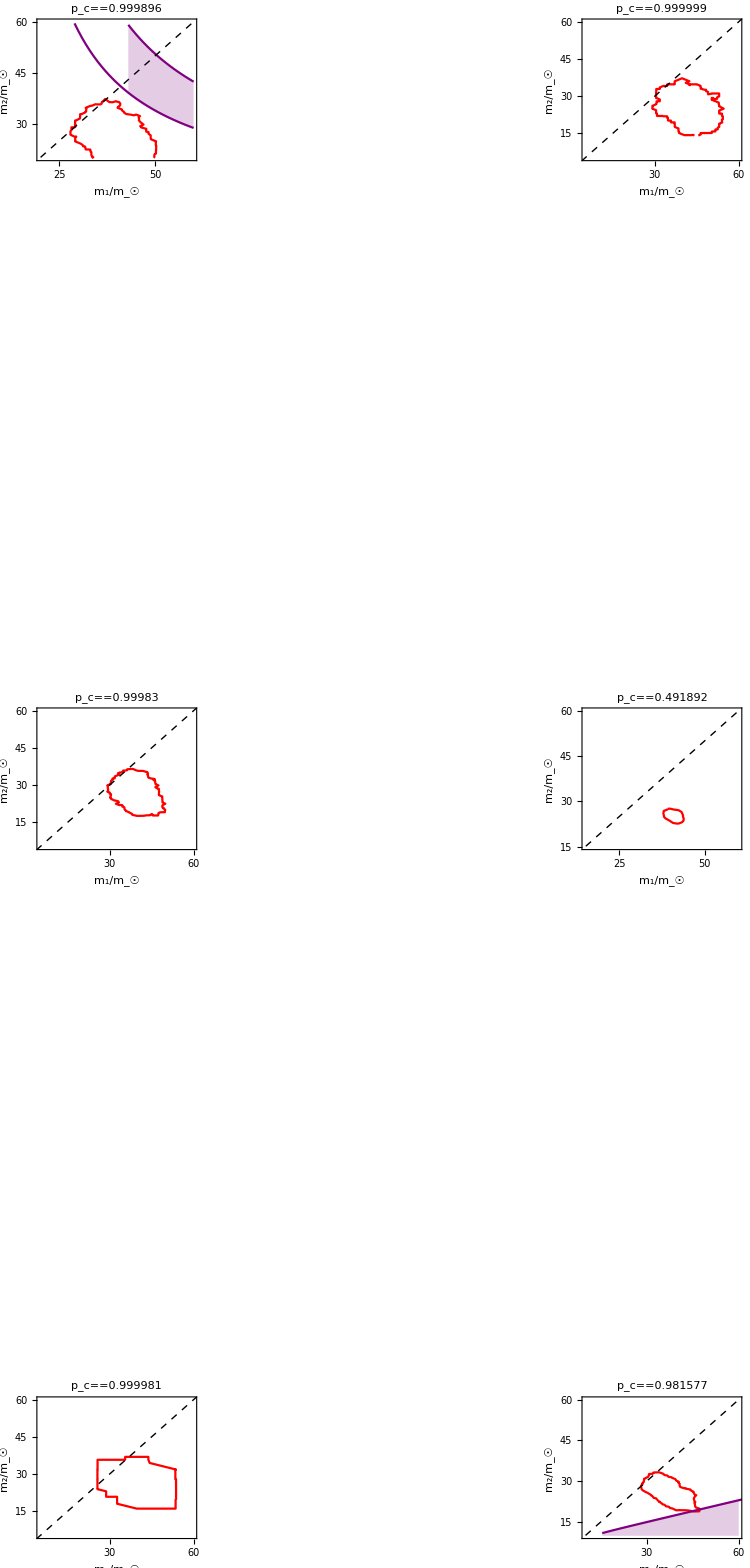

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

## (old) m1-m2 Plot, 22

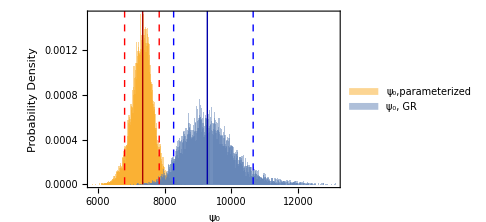

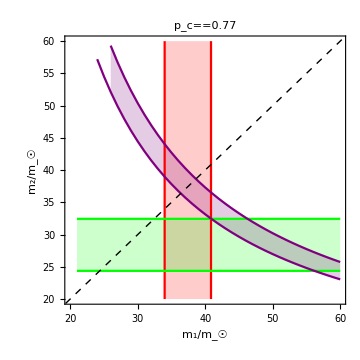

```mathematica
m1s=Range[20,60,1];
m2s=Range[20,60,1];

order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.77;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

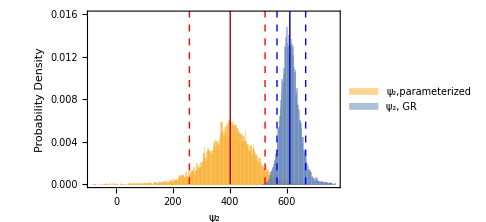

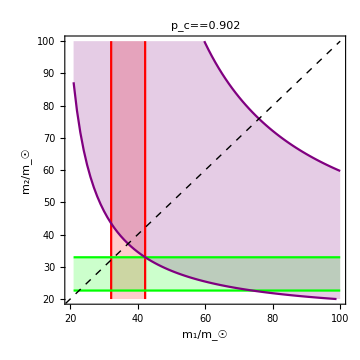

```mathematica
m1s=Range[20,100,1];
m2s=Range[20,100,1];

order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.902;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
(*Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]*)};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,2]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.902^3
```

0.266129

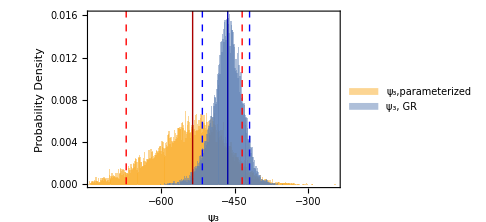

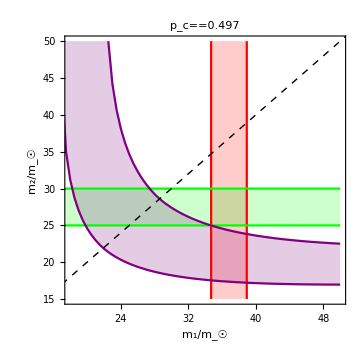

```mathematica
m1s=Range[15,50,1/2];
m2s=Range[15,50,1/2];

order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.497;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{3,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,3]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.495^3
```

0.878713

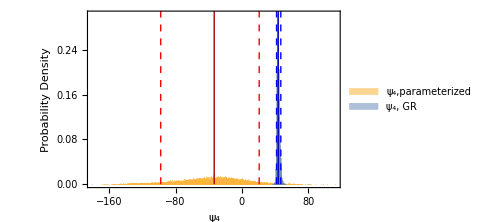

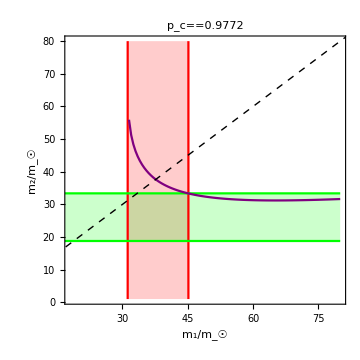

```mathematica
m1s=Range[1,80,1/2];
m2s=Range[1,80,1/2];

order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9772;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

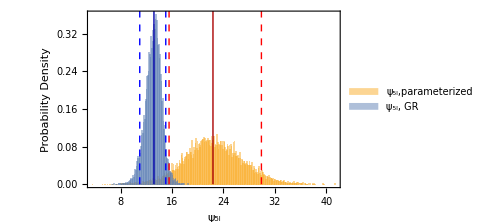

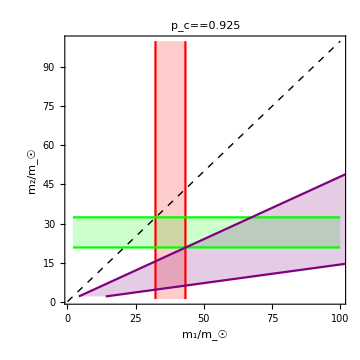

```mathematica
m1s=Range[1,100,1];
m2s=Range[1,100,1];

order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9250;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,"5l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
BCI[n][n]
```

{15.535,22.3649,29.9001}

```mathematica
1-0.925^3
```

0.208547

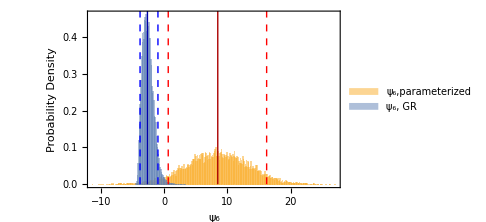

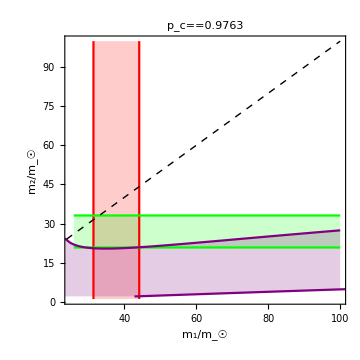

```mathematica
m1s=Range[25,100,1];
m2s=Range[1,100,1];

order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.9763;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

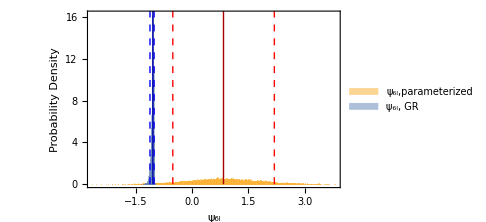

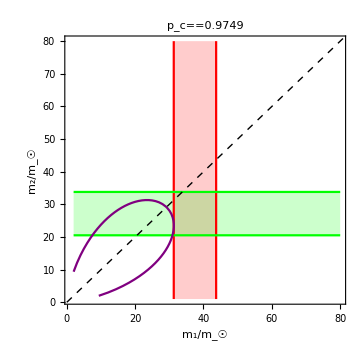

```mathematica
m1s=Range[1,80,1];
m2s=Range[1,80,1];

order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9749;
(*prob=0.9891;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Join[Reverse/@Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

Part::partw: Part 7 of … does not exist.

-Graphics-

## Value Domains

```mathematica
vd=<||>;
```

```mathematica
(BCI["cpsi0"]["cpsi0"][[3]]-BCI["cpsi0"]["cpsi0"][[1]])/5000
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[0,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi0"]["mass1"][[1]],BCI["cpsi0"]["mass1"][[3]]},
{m2,BCI["cpsi0"]["mass2"][[1]],BCI["cpsi0"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False,
AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]],TraditionalForm[Subscript[ψ,0]]}
],
{spin1z,BCI["cpsi0"]["spin1z"][[2]]},{spin2z,BCI["cpsi0"]["spin2z"][[2]]}
]
```

0.206569

```mathematica
(BCI["cpsi2"]["cpsi2"][[3]]-BCI["cpsi2"]["cpsi2"][[1]])/250
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[2,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi2"]["mass1"][[1]],BCI["cpsi2"]["mass1"][[3]]},
{m2,BCI["cpsi2"]["mass2"][[1]],BCI["cpsi2"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi2"]["spin1z"][[2]]},{spin2z,BCI["cpsi2"]["spin2z"][[2]]}
]
```

1.06474

```mathematica
(BCI["cpsi3"]["cpsi3"][[3]]-BCI["cpsi3"]["cpsi3"][[1]])/150
Manipulate[
Plot3D[
Function[{m1,m2},Psi[3,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi3"]["mass1"][[1]],BCI["cpsi3"]["mass1"][[3]]},
{m2,BCI["cpsi3"]["mass2"][[1]],BCI["cpsi3"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi3"]["spin1z"][[2]]},{spin2z,BCI["cpsi3"]["spin2z"][[2]]}
]
```

1.57419

Part::partw: Part 3 of Missing[KeyAbsent,cpsi3][mass1] does not exist.

Plot3D::plln: Limiting value mass1 in {m1,mass1,Missing[KeyAbsent,cpsi3][mass1]⟦3⟧} is not a machine-sized real number.

```mathematica
(BCI["cpsi4"]["cpsi4"][[3]]-BCI["cpsi4"]["cpsi4"][[1]])/5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[4,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi4"]["mass1"][[1]],BCI["cpsi4"]["mass1"][[3]]},
{m2,BCI["cpsi4"]["mass2"][[1]],BCI["cpsi4"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi4"]["spin1z"][[2]]},{spin2z,BCI["cpsi4"]["spin2z"][[2]]}
]
```

23.7613

```mathematica
(BCI["cpsi5l"]["cpsi5l"][[3]]-BCI["cpsi5l"]["cpsi5l"][[1]])/1.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi5l"]["mass1"][[1]],BCI["cpsi5l"]["mass1"][[3]]},
{m2,BCI["cpsi5l"]["mass2"][[1]],BCI["cpsi5l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

9.56092

```mathematica
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,3,100},
{m2,3,100},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

```mathematica
(BCI["cpsi6"]["cpsi6"][[3]]-BCI["cpsi6"]["cpsi6"][[1]])/0.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[6,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6"]["mass1"][[1]],BCI["cpsi6"]["mass1"][[3]]},
{m2,BCI["cpsi6"]["mass2"][[1]],BCI["cpsi6"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6"]["spin1z"][[2]]},{spin2z,BCI["cpsi6"]["spin2z"][[2]]}
]
```

31.1398

```mathematica
(BCI["cpsi6l"]["cpsi6l"][[3]]-BCI["cpsi6l"]["cpsi6l"][[1]])/0.1
Manipulate[
Plot3D[
Function[{m1,m2},Psi["6l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6l"]["mass1"][[1]],BCI["cpsi6l"]["mass1"][[3]]},
{m2,BCI["cpsi6l"]["mass2"][[1]],BCI["cpsi6l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6l"]["spin1z"][[2]]},{spin2z,BCI["cpsi6l"]["spin2z"][[2]]}
]
```

27.0383

```mathematica
(*Manipulate[
Plot3D[
Function[{m1,m2},Psi[7,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,20,80},
{m2,20,80},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,0.06070798549182338},{spin2z,0.09392835788044217}
(*{spin1z,-1,1},{spin2z,-1,1}*)
]*)
```

## Exports

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/comp_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,compPlots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Export["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf",patch6,"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/value_domains/","GW150914_vd_",
name,
".pdf"];
Export[exportPath,vd[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

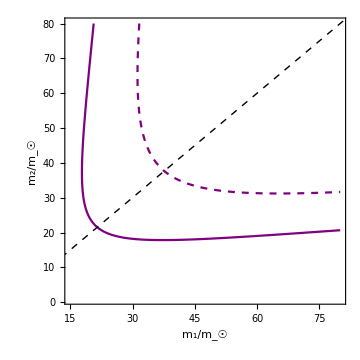

```mathematica
m1s=Range[15,80,1];
m2s=Range[1,80,1];

order=4;
n="cpsi"<>ToString[order];

prob1=0.9772;
(*再大一点会扫过这个矩形*)
prob2=0.989;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[Reverse[Reverse/@Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]]
(*tapes[n][n][[2]][[2;;]],
tapes[n][n][[4]][[2;;]]*)
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
]
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

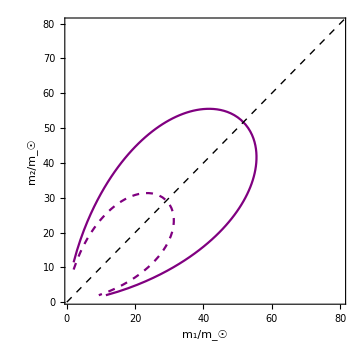

```mathematica
m1s=Range[1,80,1];
m2s=Range[1,80,1];

order="6l";
n="cpsi"<>ToString[order];

prob1=0.9749;
prob2=0.9891;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
Join[Reverse/@Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]]],
Join[Reverse/@Select[Reverse/@tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,order],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,order],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

patch6=ListLinePlot[
{
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
tapes[n][n][[1]][[2;;]],
tapes[n][n][[3]][[2;;]]
},
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},

Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
AspectRatio->1,
PlotRange->{{40.02,40.026},{30.015,30.020}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}]
},
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},

Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
],
Black,Dashed,Line[{{0,0},{100,100}}](*,
Inset[
patch6]*)
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

```mathematica
name="cpsi6l";
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
"_double",
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_inverse_plot_cpsi6l_double.pdf